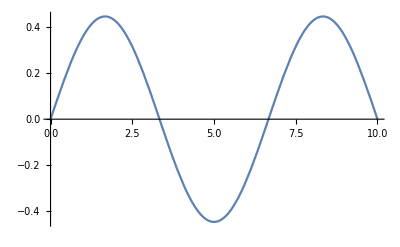

```mathematica
ψ[x_]:=√(2/L)*Sin[(nx*π)/L x];


nx=3;
L=10;

Plot[ψ[x],{x,0,10}]
```

```mathematica
Manipulate[Plot[ψ[x nx]^2,{x,0,10},PlotLegends->{nx}],{nx,1,100,1},ControlType->Slider]
```